Q^-1/ΔE (d=1.3)
with heat flow

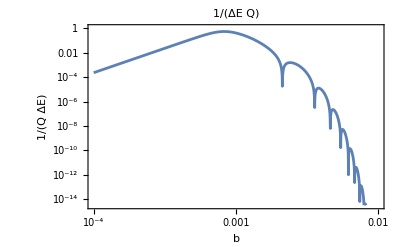

```mathematica
QHeatFlow13=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->1.3,ξ->1.24 10^6 b^2};

QHeatFlowg=LogLogPlot[QHeatFlow13,{b,0.0001,0.01},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{b,Q^-1/ΔE}]
```

```mathematica
FindArgMin[QHeatFlow13,{ξ,1,20}]
```

{5.5641}

```mathematica
FindArgMin[QHeatFlow13,{ξ,10,20}]
```

{15.8167}

```mathematica
FindArgMin[QHeatFlow13,{ξ,20,30}]
```

{26.2446}

```mathematica
FindArgMin[QHeatFlow13,{ξ,30,40}]
```

{36.9729}

```mathematica
FindArgMin[QHeatFlow13,{ξ,40,50}]
```

{47.8116}

```mathematica
FindArgMin[QHeatFlow13,{ξ,50,55}]
```

{58.2064}

```mathematica
FindArgMin[QHeatFlow13,{ξ,60,70}]
```

{68.5894}

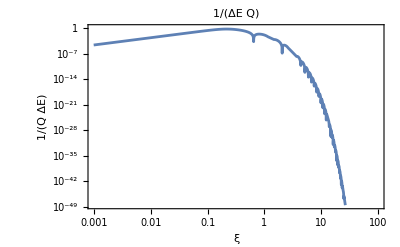

```mathematica
QHeatFlow5=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->5};

QHeatFlowg=LogLogPlot[QHeatFlow5,{ξ,0.001,100},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

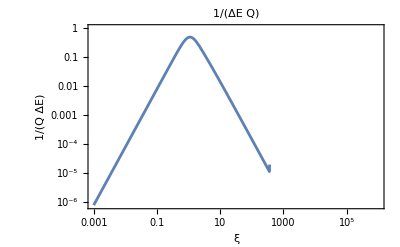

```mathematica
QHeatFlow1=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->1};

QHeatFlow1g=LogLogPlot[QHeatFlow1,{ξ,0.001,1000000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

without heat flow

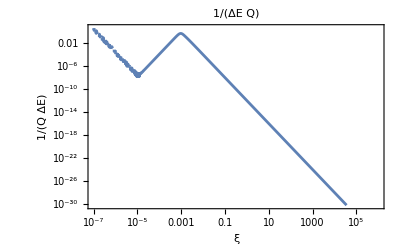

```mathematica
QNoHeatFlow =Abs[ 6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) ]/.
{ξ->1.24 10^6 b^2};

(*{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ))}/.
{ω->2π f,χ->4.47,b->2 10^-3};*)
QNoHeatFlowg=LogLogPlot[QNoHeatFlow,{b,0.0000001,1000000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

```mathematica
FullSimplify[{Abs[3/(4 ξ^3)1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))/.{d->1}]}==Abs[6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ])]]
```

True

並べる

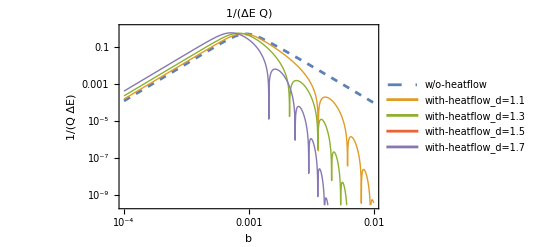

```mathematica
LogLogPlot[{QNoHeatFlow,QHeatFlow11,QHeatFlow13,QHeatFlow15,QHeatFlow17},{b,0.0001,0.01},PlotStyle->{Dashed,Thick,Thick,Thick,Thick},PlotLegends->Placed[{"w/o-heatflow","with-heatflow_d=1.1","with-heatflow_d=1.3","with-heatflow_d=1.5","with-heatflow_d=1.7"},{0.3,0.3}],PlotLabel->Q^-1/ΔE,Frame->True,FrameLabel->{b,Q^-1/ΔE},GridLinesStyle->LightGray,GridLines->Full]
```

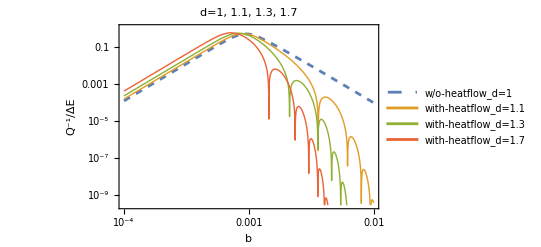

```mathematica
LogLogPlot[{QNoHeatFlow,QHeatFlow11,QHeatFlow13,QHeatFlow17},{b,0.0001,0.01},PlotStyle->{Dashed,Thick,Thick,Thick},PlotLegends->Placed[{"w/o-heatflow_d=1","with-heatflow_d=1.1","with-heatflow_d=1.3","with-heatflow_d=1.7"},{0.3,0.25}],PlotLabel->"d=1, 1.1, 1.3, 1.7",Frame->True,FrameLabel->{b,"Q^-1/ΔE"},GridLinesStyle->LightGray,GridLines->Full]
```